0.606883

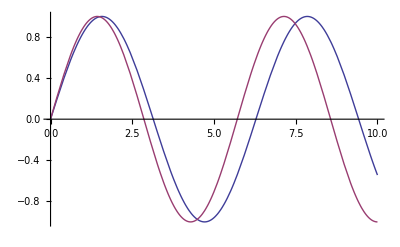

```mathematica
eps=0.1;
bench[t_]=Sin[t];
test[t_]=Sin[(1+eps)t];
Sqrt[NIntegrate[(bench[t]-test[t])^2,{t,0,10}]/NIntegrate[bench[t]^2,{t,0,10}]]

Plot[{bench[t],test[t]},{t,0,10}]
```

```mathematica
0.6068828437420661
```